```mathematica
NS["fmri_alzheimer_rgs"]
```

```mathematica
(* definition of empirical covariance matrix, used a lot in the following *)covmatrix[data_]:=Block[{means=Mean@T@data,numindividuals=Length[data[[1]]]},
((data-means).T[data-means])/numindividuals]
```

```mathematica
SetDirectory["C:\\Users\\pglpm\\repositories\\nanunana\\data_alzheimer_rgs"]
```

C:\Users\pglpm\repositories\nanunana\data_alzheimer_rgs

```mathematica
"C:\\Users\\pglpm\\repositories\\nanunana\\data_alzheimer_rgs"
```

C:\Users\pglpm\repositories\nanunana\data_alzheimer_rgs

```mathematica
<<"reference_prior.m";
```

```mathematica
fileselect="claudia"; (* "reduced" *)
categories={"alzheimer","MCI","healthy"};
categoryfiles={fileselect<>"_RGS_graphprop22_AD.txt",fileselect<> "_RGS_graphprop22_MCI.txt",fileselect<>"_RGS_graphprop22_Con.txt"};
numcategories=Length[categories];
origquantities=Flatten@Import[fileselect<>"_RGS_graphprop22_quantities.txt","CSV"];
orignumquantities=Length@origquantities;

Do[origsubjectfile[ii]=N@Import[categoryfiles[[ii]],"CSV"];numindividuals[ii]=Length[origsubjectfile[ii][[1]]],
{ii,numcategories}];
(* one row for each quantity, one column for each individual *)
minnumindividuals=Min@Table[numindividuals[ii],{ii,numcategories}];
```

```mathematica
(* improper prior *)
{referencenumber ,referencemeans,referencecovariance}= {0,Table[0,{orignumquantities}],Table[0,{orignumquantities},{orignumquantities}]};
```

```mathematica
relevant={1,2,3,8,9,12,15,16,20,21,23,24};
```

```mathematica
(* modularity is missing in the drug and schizo studies *){"graphweights1"," shortest path1"," cluster coeff.1"," shortest path2"," cluster coeff.2"," closeness centrality2"," cluster coeff.3"," weighted degree3"," shortest path4"," cluster coeff.4"," normalized weighted degree4"," closeness centrality4"}
```

```mathematica
minnumindividuals
```

14

```mathematica
orignumquantities
```

28

```mathematica
(* renormalize data for numerical stability *)

(* collect all data from all categories first *)
totaldata={};Do[totaldata=Join[totaldata,T[origsubjectfile[ii]]],{ii,numcategories}];
 (* individuals are in one column *)

tempmeans=Mean@totaldata;tempstds=Std@totaldata;
totaldata=(T@totaldata-tempmeans)/tempstds;

(* now renormalize and standardize *)
Do[origsubjectfile[ii]=(origsubjectfile[ii]-tempmeans)/tempstds,{ii,numcategories}]

(* renormalize and standardize reference prior parameters *)
referencemeans=(referencemeans-tempmeans)/tempstds;
referencecovariance=DiagonalMatrix[1/tempstds].referencecovariance.DiagonalMatrix[1/tempstds];
```

```mathematica
(* a look at the eigenvectors and eigenvalues of the empirical covariance matrix *)
T@Eigensystem[covmatrix[totaldata]]//MF
```

(11.2119 | {-0.235263,0.227326,-0.255074,-0.0884977,-0.00513543,-0.101524,-0.253669,0.134022,-0.260424,0.185665,-0.258046,-0.202677,-0.14417,-0.280734,-0.202754,-0.136377,0.224122,-0.132909,-0.162438,-0.204012,-0.239213,0.138389,-0.217278,-0.123757,-0.139644,-0.243916,0.0477319,-0.0458034}
4.7505 | {0.200994,-0.247442,0.130825,0.0906947,0.043535,0.232766,0.173394,-0.101463,0.105033,-0.265427,-0.203713,0.0739467,-0.299719,-0.0768201,0.0175555,0.257153,0.264044,0.0181292,-0.239153,-0.287292,0.0763106,-0.254191,-0.266278,0.0482923,-0.262039,-0.227978,-0.108668,0.00897724}
3.39621 | {-0.12843,0.115259,-0.123884,0.0634486,-0.381206,0.224688,-0.100344,0.311787,-0.0255587,0.124341,0.00581156,0.350247,-0.0458972,0.0219697,0.317386,-0.0761192,0.0401702,0.397906,-0.0202428,-0.0824369,0.0719251,0.108901,-0.0661052,0.415509,-0.0686446,-0.0535229,-0.00546049,-0.176133}
2.26486 | {0.165493,0.11318,0.130805,0.265132,0.188278,-0.161232,0.117866,-0.0022957,0.200947,0.255963,0.0224286,-0.0456685,-0.236282,0.130717,0.101918,-0.263675,-0.0398247,-0.102022,-0.306584,-0.0170316,0.282651,0.298145,0.0582552,-0.0729406,-0.306471,0.0927209,0.246911,-0.297459}
1.5409 | {0.130348,0.0107723,0.11107,-0.411557,0.336514,-0.12215,0.122919,-0.241933,0.0968756,0.14665,-0.0564532,0.155356,0.0810692,-0.0533618,-0.0567436,-0.304506,0.13314,0.290665,0.055644,-0.123197,0.0731574,0.266316,-0.155769,0.270547,0.072844,-0.131525,-0.0324224,0.343393}
1.0221 | {0.0384988,-0.00133401,0.0468861,0.402795,-0.195891,0.151937,0.0691855,-0.00251151,0.0901964,0.0497506,-0.123272,0.0247235,0.258174,0.0203932,0.113793,-0.151052,0.215136,-0.229327,0.287348,-0.25685,0.180989,0.132267,-0.224614,-0.201424,0.331637,-0.130845,0.276866,0.214758}
0.936282 | {-0.0862404,-0.00554087,-0.0365128,0.181336,0.304385,0.0631084,-0.106772,-0.327543,-0.182024,-0.107593,-0.0320506,0.120443,0.161095,-0.0711512,-0.100108,0.102491,-0.0204879,0.205647,-0.00953954,0.0249327,-0.15856,-0.163037,-0.0079593,0.213586,0.0608288,-0.0337618,0.639702,-0.276275}
0.849148 | {0.0794698,-0.0887891,0.0856899,-0.423032,-0.246852,-0.398698,0.0868883,0.378963,0.112263,-0.0663182,0.00399019,-0.128402,0.00938957,0.0328642,0.0641217,0.197948,0.0464168,0.0355597,-0.055825,-0.0506426,0.113163,-0.153216,-0.0530842,-0.0147114,0.00249436,-0.0326521,0.54254,0.081487}
0.657502 | {-0.0868816,0.0553208,-0.12179,0.0603489,-0.100544,0.298697,-0.0914772,-0.094369,-0.0365352,0.0476769,0.114481,0.051836,-0.0280224,0.0604219,0.00761227,0.0340897,-0.146696,-0.0412201,-0.306793,0.0856238,-0.0372963,0.0327923,0.143793,-0.0267717,-0.323708,0.0616883,0.271947,0.705817}
0.441304 | {0.215571,-0.0265575,0.258167,-0.271315,-0.169869,0.531537,0.173796,0.161704,-0.0120986,0.0806912,-0.0321154,0.124819,-0.0323745,-0.00922071,-0.476213,-0.0831585,-0.0459318,-0.0910494,0.0579679,0.153638,-0.170664,0.201427,0.0154873,-0.0964485,0.00147331,-0.00963986,0.166111,-0.205991}
0.233038 | {0.0946195,-0.120275,0.164484,0.438532,0.176021,-0.18547,0.0527642,0.485765,-0.101648,-0.160402,-0.0141301,-0.0103735,-0.227377,-0.19617,-0.253089,-0.239377,-0.0482273,0.153541,0.170582,0.135131,-0.131067,-0.0730499,0.0508809,0.194819,-0.00120824,0.00779272,0.0129158,0.261971}
0.18407 | {-0.0106298,-0.106243,-0.137806,-0.0085721,-0.266505,-0.0555384,0.0575634,-0.368631,0.0357459,-0.0103519,0.0460597,-0.162093,-0.643135,-0.118189,0.0716259,0.101084,-0.0296477,0.0628125,0.403842,0.0695809,-0.0652882,0.263925,0.0770362,0.0541575,0.0679578,-0.0203426,0.149484,0.0241978}
0.141595 | {0.078595,0.17055,0.13894,0.243973,-0.0848686,-0.207276,0.0465568,-0.0183855,-0.012146,0.296353,-0.110132,0.0522373,0.0876022,0.0127699,-0.300633,0.665537,0.000731256,0.102989,-0.148326,0.00709042,0.0122142,0.300866,-0.0372842,0.144441,0.14752,0.034465,-0.109837,0.0930284}
0.119853 | {0.0296834,-0.486372,0.0537546,0.116764,-0.298783,-0.278295,0.120661,-0.148378,-0.0863791,-0.0558489,0.0354282,0.0608626,0.235842,0.162796,0.0827047,-0.166601,0.0194193,0.010385,-0.218411,0.0111559,-0.52055,0.250625,-0.0614854,-0.0138042,-0.122505,-0.0723987,-0.042591,-0.0484961}
0.0811027 | {0.0397985,0.174015,0.437766,-0.0454179,-0.139204,-0.0735293,-0.151924,-0.143306,-0.505475,-0.0501006,-0.409833,-0.0418933,-0.0855192,0.388752,0.0913898,-0.0861559,-0.0680864,0.0310242,0.153216,0.0496087,0.0944921,-0.0941191,-0.104017,-0.00114802,-0.147533,0.133952,-0.017684,0.0625845}
0.0629276 | {0.0467481,0.243467,0.0145511,0.0857509,-0.244958,-0.200355,0.0228396,-0.175279,0.15543,0.0102372,0.224408,0.102577,0.236924,-0.092749,-0.292463,-0.0373809,-0.0274457,0.0623743,0.37608,-0.0640854,0.0705391,-0.183034,-0.0216705,-0.036499,-0.568922,-0.2117,-0.0429035,-0.044449}
0.0459638 | {-0.034837,-0.024519,0.043847,-0.0668379,0.410991,0.0455239,-0.0779435,0.261062,-0.104458,-0.101198,0.169183,0.213702,-0.00249963,0.130596,0.280723,0.328604,-0.00808174,-0.0692303,0.350212,-0.0932824,-0.187686,0.358275,-0.113898,-0.225986,-0.279955,-0.0565258,0.0423845,0.00921473}
0.0224827 | {0.0322899,-0.13056,-0.000940521,-0.00580696,-0.000171869,0.189378,0.0123365,0.0434219,-0.00590914,-0.212119,-0.242636,-0.560237,0.360148,-0.256449,0.098818,0.0690182,0.0233728,0.0934572,0.0892381,0.0208682,0.176887,0.318816,0.176932,0.223998,-0.268096,0.100236,-0.0132206,-0.0449124}
0.0152564 | {-0.0586148,0.0419968,-0.295926,0.039327,0.0828021,0.0721496,0.0617818,0.0657439,0.261643,0.0481629,-0.0478062,-0.221486,-0.0199871,0.542903,-0.186517,-0.00307597,0.412444,0.0473191,0.146177,0.126368,-0.184138,-0.0822181,-0.210526,0.176426,-0.104823,0.309486,0.0221176,0.0190471}
0.00723527 | {-0.0542022,-0.238021,-0.139595,-0.041132,0.0482894,-0.0973165,0.0159569,0.00492786,0.173105,0.283353,-0.574779,0.390475,0.0460436,-0.192063,0.0976092,0.0471595,0.0439216,-0.2539,0.170611,0.286524,0.00341586,-0.122645,0.17676,0.0229306,-0.167956,0.0981411,0.02425,0.0210003}
0.00482212 | {0.107732,-0.348264,-0.000760659,0.00220787,0.0915896,0.120078,-0.0283973,0.0620866,-0.1561,0.606251,0.105726,-0.247782,-0.00375731,0.135914,0.000840615,0.038941,-0.205925,-0.0278883,0.164472,-0.40451,-0.0447421,-0.252169,0.138304,0.159734,-0.0464393,-0.0941035,-0.00588254,-0.00200642}
0.00435575 | {-0.262599,-0.364491,-0.230931,-0.0470112,-0.0234938,-0.093779,-0.0924467,0.0154897,-0.179551,-0.223469,0.0281824,0.233803,-0.035052,0.156172,-0.423593,-0.0313091,-0.100986,-0.127418,0.0041394,-0.261254,0.454546,0.197858,-0.0129246,0.0674379,-0.0283199,0.182527,-0.00781181,-0.0386276}
0.00237282 | {-0.0677644,-0.322851,-0.0208398,0.0407992,0.0179302,0.0580944,-0.0623828,-0.00904876,-0.174849,0.266383,0.162703,-0.0991915,0.0332742,-0.108503,-0.00142858,0.0276564,0.0988317,0.327514,-0.0132627,0.489862,0.309612,-0.041513,-0.410769,-0.315265,-0.0520482,-0.0639805,-0.0136906,-0.00681935}
0.00185452 | {0.0940276,-0.00533237,-0.256154,0.0390837,0.0639502,0.0120773,-0.0939165,0.068704,0.176565,-0.125807,-0.304429,-0.0775454,0.000553201,0.391285,-0.0844984,-0.00134379,-0.337623,0.181708,-0.00948154,0.144574,0.0649744,0.0706313,0.111196,-0.108671,0.0764399,-0.626755,-0.0131076,-0.00728168}
0.00118821 | {-0.150519,0.0234743,-0.0359062,0.0239997,-0.00395095,0.0264775,0.166264,0.00685963,0.211125,0.0122623,-0.268485,-0.00567813,-0.00420371,-0.0963782,-0.0380907,-0.0298677,-0.350668,0.474601,0.0195245,-0.327269,-0.151665,-0.0396063,-0.117219,-0.420677,-0.0156927,0.383021,0.00614619,0.00781525}
0.000802409 | {-0.00993365,-0.142329,0.244617,0.00979494,-0.0247851,0.00275796,-0.504288,-0.0170113,0.168572,0.0162595,0.0143637,0.0506546,-0.0384882,0.0556496,-0.0918925,-0.00710451,0.458054,0.285849,-0.0074803,-0.114224,0.0025788,0.0258763,0.49341,-0.264948,0.0317657,0.000116112,-0.00158109,0.00162646}
0.000234923 | {-0.0198263,0.109195,-0.234122,0.0112298,0.0280667,-0.0188958,0.617956,0.030404,-0.426266,0.0227571,-0.0123274,0.0610809,0.023278,0.0730242,0.0207486,0.0142224,0.309616,0.178634,-0.000272017,-0.0296215,0.0819211,-0.0314555,0.412824,-0.203558,-0.0151043,-0.0879635,0.000289492,0.00433955}
0.0000970729 | {-0.792753,-0.032362,0.419857,0.00215044,0.0491059,0.0497739,0.248187,0.0050358,0.184606,0.0540597,0.00840936,-0.101463,-0.0407361,0.0762709,-0.0156702,0.0151051,-0.00329489,-0.0562726,-0.000134054,0.0515767,0.000778859,-0.0139084,0.052677,0.0934037,-0.0120708,-0.233872,-0.00282026,-0.00152434})

```mathematica
Det[covmatrix[totaldata]]
```

1.26769×10^-34

```mathematica
(* some analysis shows that selecting eigenvector seems to be a bad idea *)eigenvectors=T[Eigenvectors[covmatrix[totaldata]]];
ieigenvectors=Inverse[eigenvectors];

Do[origsubjectfile[ii]=ieigenvectors.origsubjectfile[ii],{ii,numcategories}];
totaldata=ieigenvectors.totaldata;

referencemeans=ieigenvectors.referencemeans;
referencecovariance=ieigenvectors.referencecovariance.eigenvectors;
```

```mathematica
(* we can use at most (num.subjects -2) quantities. We choose those that have the covariance matrix with largest volume *)

(* this selects all possible subsets of (num.subjs-2) quantities out of all available quantities *)
(*numusedquantities=minnumindividuals-2;*)
numusedquantities=24;

trialquantities=Subsets[Range[orignumquantities],{numusedquantities}];
totcovmatrix=covmatrix[totaldata];

(* this calculates all determinants of cov. matrices for these subsets *)
trialdeterminants=Table[Abs@Det[totcovmatrix[[ii,ii]]],{ii,trialquantities}];

(* this is the subset with largest scatter *)
bestquantities=Ordering[trialdeterminants,-1][[1]];
chosenquantities=trialquantities[[bestquantities]];
ClearAll[trialquantities,trialdeterminants];
origquantities[[chosenquantities]]
```

{graphweights1, shortest path1, cluster coeff.1, weighted degree1, normalized weighted degree1, closeness centrality1, graphweights2, shortest path2, cluster coeff.2, weighted degree2, normalized weighted degree2, closeness centrality2, graphweights3, shortest path3, cluster coeff.3, weighted degree3, normalized weighted degree3, closeness centrality3, graphweights4, shortest path4, cluster coeff.4, weighted degree4, normalized weighted degree4, closeness centrality4}

```mathematica
relevant={1,2,3,8,9,12,15,16,20,21,23,24}
```

{1,2,3,8,9,12,15,16,20,21,23,24}

```mathematica
chosenquantities=relevant
```

{1,2,3,8,9,12,15,16,20,21,23,24}

```mathematica
chosenquantities={1,2,3,7,10,13,14,18,19,21,22};
```

```mathematica
qqq=Sort@RandomSample[relevant,3];Print[qqq];
ListPointPlot3D[Evaluate@Table[origsubjectfile[ii][[qqq]],{ii,3}],BoxRatios->1,PlotStyle->{{PointSize[Large],red},{PointSize[Large],blue},{PointSize[Large],green}},PlotRange->All,ViewPoint->Dynamic[viewpoint],AxesLabel->myaxes[origquantities[[qqq]]]]
```

```mathematica
expng["discrete_quantities"]
```

./discrete_quantities.png

```mathematica
(* select subsets of data, for each category, corresponding to the optimal quantities *)
quantities=origquantities[[chosenquantities]];numquantities=Length@quantities;
Do[subjectfile[ii]=origsubjectfile[ii][[chosenquantities]],{ii,numcategories}];

nreferencemeans=referencemeans[[chosenquantities]];
nreferencecovariance=referencecovariance[[chosenquantities,chosenquantities]];
```

```mathematica
Do[means[ii]=Mean@T@subjectfile[ii];
tparameter[ii]=numindividuals[ii]+1-numquantities;
tcovariance[ii]=covmatrix[ subjectfile[ii]];
,{ii,numcategories}];
```

```mathematica
Table[Det@tcovariance[ii],{ii,numcategories}]
```

{1.00057×10^-27,2.16282×10^-23,1.54773×10^-13}

```mathematica
Det@nreferencecovariance
```

0.

```mathematica
(* we show the two distributions in a 2D section of the (numquantities)-dimensional space. This section is chosen this way:
the centroids of the three distributions are on three sides of an equilateral triangle;


This section is represented by a (numquantities x 3)-dimensional matrix; it has 3 columns because it's an affine transformation *)
```

```mathematica
(* matrix of the target vectors in the 3D section *)
centreh={0,0,1};centrea={Cos[2*Pi/3],Sin[2*Pi/3],1};centrem={Cos[Pi/3],Sin[Pi/3],1};
targetvectors=T@{centrea,centreh,centrem};

(* matrix of the vectors to appear in the 3D section *)
originalvectors = T@{means[1],means[2],means[3]};

(* section matrix *)
sectionmatrix=originalvectors.Inverse[targetvectors];
```

```mathematica
(* define the distribution in the 2D section *)Do[distribution[ii,x_,y_]=PDF[MultivariateTDistribution[means[ii],tcovariance[ii]*(numindividuals[ii]+1)/tparameter[ii],tparameter[ii]],FS[sectionmatrix.{x,y,1}]],{ii,numcategories}];
```

```mathematica
{maxa,maxm,maxh}=Table[Maximize[distribution[ii,x,y],{x,y}][[1]],{ii,numcategories}]
```

{6.09562×10^6,97826.1,6.23838}

```mathematica
totdistr[x_,y_]=Sum[1/3*PDF[MultivariateTDistribution[means[ii],tcovariance[ii]*(numindividuals[ii]+1)/tparameter[ii],tparameter[ii]],FS[sectionmatrix.{x,y,1}]],{ii,numcategories}];
```

```mathematica
Maximize[totdistr[x,y],{x,y}]
```

{2.07946,{x→0.5,y→0.866025}}

```mathematica
Maximize[Sum[1/3*PDF[MultivariateTDistribution[means[ii],tcovariance[ii]*(numindividuals[ii]+1)/tparameter[ii],tparameter[ii]],vector],{ii,numcategories}],vector,Reals]
```

{2.07946,{x[1]→0.243769,x[2]→-0.320758,x[3]→0.214315,x[4]→-0.197737,x[5]→0.170497,x[6]→0.169121,x[7]→-0.0331808,x[8]→0.129132,x[9]→-0.0502454,x[10]→0.0382272,x[11]→-0.106114,x[12]→0.150845}}

```mathematica
myfontsize=24;rangex=1;rangey=2;Plot3D[Evaluate@Join[Table[distribution[ii,x,y],{ii,numcategories}],{totdistr[x,y]}],{x,-1,2},{y,-1,3},AxesLabel->{None,None,pdf},PlotRange->{0,7},Ticks->{None,None,Auto},PlotStyle->{{red,Opacity[0.75]},{blue,Opacity[0.75]},{green,Opacity[0.75]},{Black,Opacity[0.75]}},PlotPoints->75,Mesh->None,BoxRatios->{1,1,1/GoldenRatio},PlotLegends->mylegendsc[{{red,Thickness[1]},{green,Thickness[1]},{blue,Thickness[1]}},{Alzheimer,Healthy,"Cog. impaired"}],ViewPoint->Dynamic[viewpoint],Lighting->"Ambient"]
```

```mathematica
myfontsize=24;rangex=1;rangey=2;Plot3D[Evaluate@Table[distribution[ii,x,y],{ii,numcategories}],{x,-1,2},{y,-1,3},AxesLabel->{None,None,pdf},PlotRange->{0,maxh},Ticks->{None,None,Auto},PlotStyle->{{red,Opacity[0.75]},{blue,Opacity[0.75]},{green,Opacity[0.75]}},PlotPoints->100,Mesh->None,BoxRatios->{1,1,1/GoldenRatio},PlotLegends->mylegendsc[{{red,Thickness[1]},{green,Thickness[1]},{blue,Thickness[1]}},{Alzheimer,Healthy,"Cog. impaired"}],ViewPoint->Dynamic[viewpoint],Lighting->"Ambient"]
```

```mathematica
light=viewpoint
```

{-0.176728,2.97119,1.60959}

```mathematica
expng["testplot_talk3"];
```

```mathematica
expdfr["testplot_talk",%79];
```

```mathematica
expdfr["testplot_talk",%%]
```

./testplot_talk.pdf

```mathematica
(* study of likelihood *)
likelihood[vector_]:=Normalize [Table[PDF[MultivariateTDistribution[means[ii],tcovariance[ii]*(numindividuals[ii]+1)/tparameter[ii],tparameter[ii]],vector],{ii,numcategories}],Total]
```

```mathematica
(* study of likelihood *)
vector=Array[x,numquantities];ClearAll[KLd];
KLd[vector_]:=-likelihood[vector].Log[likelihood[vector]*3];
```

```mathematica
findmax=NMaximize[Sum[Log@likelihood[vector][[ii]],{ii,numcategories}],vector,Reals]
```

{-3.29584,{x[1]→0.829875,x[2]→0.399563,x[3]→-0.742327,x[4]→0.419738,x[5]→-0.0538171,x[6]→-0.850636,x[7]→-0.985619,x[8]→0.458062,x[9]→-2.11185,x[10]→0.765827,x[11]→3.03442,x[12]→0.281476}}

```mathematica
maximuml=vector/.findmax[[2]]
```

{0.829875,0.399563,-0.742327,0.419738,-0.0538171,-0.850636,-0.985619,0.458062,-2.11185,0.765827,3.03442,0.281476}

```mathematica
KLd[maximuml]
```

-7.28558×10^-15

```mathematica
likelihood[maximuml]
```

{0.333333,0.333333,0.333333}

```mathematica
(* matrix of the target vectors in the 3D section *)
targetvectors={{-1,1,0},{0,0,1},{1,1,1}};

(* matrix of the vectors to appear in the 3D section *)
originalvectors = T@{means[1],means[3],maximuml};

(* section matrix *)
sectionmatrix=originalvectors.Inverse[targetvectors];
```

```mathematica
distribution2[x_,y_]=likelihood[FS[sectionmatrix.{x,y,1}]];
```

```mathematica
{maxa2,maxm2,maxh2}=Table[Maximize[distribution2[x,y][[ii]],{x,y}],{ii,numcategories}]
```

{{0.999985,{x→4.59695,y→1.25049}},{1.,{x→-193.472,y→-16.3959}},{1.,{x→0.288472,y→-0.0278281}}}

```mathematica
totdistr[x_,y_]=Sum[1/3*PDF[MultivariateTDistribution[means[ii],tcovariance[ii]*(numindividuals[ii]+1)/tparameter[ii],tparameter[ii]],FS[sectionmatrix.{x,y,1}]],{ii,numcategories}];
```

```mathematica
Maximize[totdistr[x,y],{x,y}]
```

{2.07946,{x→1.,y→1.16675×10^-16}}

```mathematica
myfontsize=24;rangex=3/2;rangey=1/2;Plot3D[totdistr[x,y]/2.08,{x,-2,2},{y,-1,2},AxesLabel->{None,None,None},PlotRange->{0,1.1},Ticks->{None,None,Auto},PlotStyle->{{red,Opacity[0.75]},{blue,Opacity[0.75]},{green,Opacity[0.75]},{Black,Opacity[0.75]}},PlotPoints->75,Mesh->None,BoxRatios->{1,1,1/GoldenRatio},PlotLabel->With[{myfontsize=12},mylabels[{"P"[condition|"graph properties"]}]],PlotLegends->mylegendsc[{{red,Thickness[1]},{green,Thickness[1]},{blue,Thickness[1]}},{Alzheimer,Healthy,"Cog. impaired"}],ViewPoint->Dynamic[viewpoint],Lighting->"Ambient"]
```

```mathematica
myfontsize=24;rangex=3/2;rangey=1/2;Plot3D[Evaluate@Join[distribution2[x,y],{totdistr[x,y]/2.08}],{x,-1.1,1.1},{y,-0.1,1.1},AxesLabel->{None,None,None},PlotRange->{0,1.1},Ticks->{None,None,Auto},PlotStyle->{{red,Opacity[0.75]},{blue,Opacity[0.75]},{green,Opacity[0.75]},{Black,Opacity[0.75]}},PlotPoints->75,Mesh->None,BoxRatios->{1,1,1/GoldenRatio},PlotLabel->With[{myfontsize=12},mylabels[{"P"[condition|"graph properties"]}]],PlotLegends->mylegendsc[{{red,Thickness[1]},{green,Thickness[1]},{blue,Thickness[1]}},{Alzheimer,Healthy,"Cog. impaired"}],ViewPoint->Dynamic[viewpoint],Lighting->"Ambient"]
```

```mathematica
expng["plot_likelihood3"]
```

./plot_likelihood3.png

```mathematica
(* we show the two distributions in a 2D section of the (numquantities)-dimensional space. This section is chosen this way:
1. the centroids of AD and healthy  have coords (-1,0) and (1,0);
2. point of max overlap of the distributions, intended as Log[p1*p2] (where they must be equal) has coords (0,1).

This section is represented by a (numquantities x 3)-dimensional matrix; it has 3 columns because it's an affine transformation *)
```

```mathematica
(* overlap function Log[p1*p2] *)
vector=Array[x,numquantities];
KLd[vector_]=
Sum[PDF[MultivariateTDistribution[means[ii],tcovariance[ii]*(numindividuals[ii]+1)/tparameter[ii],tparameter[ii]],vector]*Log[PDF[MultivariateTDistribution[means[ii],tcovariance[ii]*(numindividuals[ii]+1)/tparameter[ii],tparameter[ii]],vector]],{ii,numcategories}];
```

```mathematica
(* find the maximum *)findmax=Maximize[KLd[vector],vector,Reals]
```

{-1.36245×10^-27,{x[1]→0.801282,x[2]→-1.09771,x[3]→0.47761,x[4]→-0.29988,x[5]→-0.411704,x[6]→-0.278051,x[7]→-0.227313,x[8]→-0.426448,x[9]→-1.69964,x[10]→1.24606,x[11]→1.70018,x[12]→0.741748}}

```mathematica
maximum=vector/.findmax[[2]]
```

{0.801282,-1.09771,0.47761,-0.29988,-0.411704,-0.278051,-0.227313,-0.426448,-1.69964,1.24606,1.70018,0.741748}

```mathematica
(* overlap function Log[p1*p2] *)
vector=Array[x,numquantities];
overlap[vector_]=
Sum[Log@PDF[MultivariateTDistribution[means[ii],tcovariance[ii]*(numindividuals[ii]+1)/tparameter[ii],tparameter[ii]],vector],{ii,numcategories}];
```

```mathematica
(* find the maximum *)findmax=NMaximize[overlap[vector],vector,Reals]
```

{26.5741,{x[1]→-0.461234,x[2]→0.507978,x[3]→-0.456076,x[4]→0.174862,x[5]→-0.514128,x[6]→-0.400557,x[7]→-0.351192,x[8]→-0.249913,x[9]→-0.167336,x[10]→-0.385019,x[11]→-0.161947,x[12]→-0.192026}}

```mathematica
maximum=vector/.findmax[[2]]
```

{-0.461234,0.507978,-0.456076,0.174862,-0.514128,-0.400557,-0.351192,-0.249913,-0.167336,-0.385019,-0.161947,-0.192026}

```mathematica
Table[PDF[MultivariateTDistribution[means[ii],tcovariance[ii]*(numindividuals[ii]+1)/tparameter[ii],tparameter[ii]],maximum],{ii,numcategories}]
```

{3.14117×10^6,49130.9,2.25189}

```mathematica
(* matrix of the target vectors in the 3D section *)
targetvectors={{-1,1,0},{0,0,1},{1,1,1}};

(* matrix of the vectors to appear in the 3D section *)
originalvectors = T@{means[1],means[3],maximum};

(* section matrix *)
sectionmatrix=originalvectors.Inverse[targetvectors];
```

```mathematica
(* define the distribution in the 2D section *)distribution2[x_,y_]=likelihood[FS[sectionmatrix.{x,y,1}]]
```

```mathematica
Table[Maximize[distribution2[ii,x,y],{x,y}],{ii,numcategories}]
```

{{6.09562×10^6,{x→-1.,y→-6.9492×10^-18}},{2.69819×10^-8,{x→1.39549,y→-0.0673293}},{6.23838,{x→1.,y→1.55468×10^-18}}}

```mathematica
{maxa2,maxm2,maxh2}=Table[Maximize[distribution2[ii,x,y],{x,y}][[1]],{ii,numcategories}]
```

{6.09562×10^6,2.69819×10^-8,6.23838}

```mathematica
rangex=5;rangey=1;Plot3D[Evaluate@Table[distribution2[ii,x,y],{ii,numcategories}],{x,-rangex,rangex},{y,-rangey,rangey},AxesLabel->{"param 1","param 2",pdf},PlotRange->{0,maxh2},Ticks->{Auto,Auto,Auto},PlotStyle->{{red,Opacity[0.75]},{blue,Opacity[0.75]},{green,Opacity[0.75]}},PlotPoints->Auto,Mesh->None,BoxRatios->{1,1,1/GoldenRatio},PlotLegends->mylegends[{Alzheimer,"Cog. impaired",Healthy}],ViewPoint->Dynamic[viewpoint]]
```

```mathematica
rangex=5;rangey=5;Plot3D[{distribution[1,x,y],distribution[2,x,y]},{x,-rangex,rangex},{y,-rangey,rangey},AxesLabel->{x,y,P},PlotRange->All,PlotStyle->{{red,Opacity[0.75]},{blue,Opacity[0.75]}},PlotPoints->75,Mesh->None,BoxRatios->{1,1,1/GoldenRatio},PlotLegends->mylegends[categories],ViewPoint->Dynamic[viewpoint]]
```

```mathematica
(* study of likelihood *)
likelihood[vector_]:=Normalize [Table[PDF[MultivariateTDistribution[means[ii],tcovariance[ii]*(numindividuals[ii]+1)/tparameter[ii],tparameter[ii]],vector],{ii,numcategories}],Total]
```

```mathematica
(* study of likelihood *)
vector=Array[x,numquantities];ClearAll[KLd];
KLd[vector_]:=-likelihood[vector].Log[likelihood[vector]*3];
```

```mathematica
findmax=NMaximize[Sum[Log@likelihood[vector][[ii]],{ii,numcategories}],vector,Reals]
```

{-3.29584,{x[1]→0.829875,x[2]→0.399563,x[3]→-0.742327,x[4]→0.419738,x[5]→-0.0538171,x[6]→-0.850636,x[7]→-0.985619,x[8]→0.458062,x[9]→-2.11185,x[10]→0.765827,x[11]→3.03442,x[12]→0.281476}}

```mathematica
maximuml2=vector/.findmax[[2]]
```

{0.829875,0.399563,-0.742327,0.419738,-0.0538171,-0.850636,-0.985619,0.458062,-2.11185,0.765827,3.03442,0.281476}

```mathematica
KLd[maximuml2]
```

-7.28558×10^-15

```mathematica
(* find the maximum *)findmax=NMaximize[KLd[vector],vector,Reals]
```

{-0.405465,{x[1]→-0.582914,x[2]→0.624809,x[3]→-0.0169292,x[4]→-0.000621722,x[5]→-0.210497,x[6]→0.141404,x[7]→-0.39762,x[8]→-0.557158,x[9]→-0.781403,x[10]→0.436014,x[11]→0.864055,x[12]→-0.593852}}

```mathematica
maximuml=vector/.findmax[[2]]
```

{0.829875,0.399563,-0.742327,0.419738,-0.0538171,-0.850636,-0.985619,0.458062,-2.11185,0.765827,3.03442,0.281476}

```mathematica
likelihood[maximuml2]
```

{0.333333,0.333333,0.333333}

```mathematica
(* matrix of the target vectors in the 3D section *)
targetvectors={{-1,1,0},{0,0,1},{1,1,1}};

(* matrix of the vectors to appear in the 3D section *)
originalvectors = T@{means[1],means[3],maximuml2};

(* section matrix *)
sectionmatrix=originalvectors.Inverse[targetvectors];
```

```mathematica
(* define the distribution in the 2D section *)Do[distribution2[ii,x_,y_]=PDF[MultivariateTDistribution[means[ii],tcovariance[ii]*(numindividuals[ii]+1)/tparameter[ii],tparameter[ii]],FS[sectionmatrix.{x,y,1}]],{ii,numcategories}];
```

```mathematica
Table[Maximize[distribution2[ii,x,y],{x,y}],{ii,numcategories}]
```

{{6.09562×10^6,{x→-1.,y→-7.39374×10^-18}},{6.89858×10^-9,{x→1.33524,y→-0.0445316}},{6.23838,{x→1.,y→4.71754×10^-18}}}

```mathematica
Table[distribution2[ii,0,1],{ii,numcategories}]
```

{1.66278×10^-33,1.66278×10^-33,1.66278×10^-33}

```mathematica
{maxa2,maxm2,maxh2}=Table[Maximize[distribution2[ii,x,y],{x,y}][[1]],{ii,numcategories}]
```

{6.09562×10^6,6.89858×10^-9,6.23838}

```mathematica
rangex=3/2;rangey=1/2;Plot3D[Evaluate@Table[distribution2[ii,x,y],{ii,numcategories}],{x,-rangex,rangex},{y,-1/2,3/2},AxesLabel->{"param 1","param 2",pdf},PlotRange->{0,2*10^-33},Ticks->{Auto,Auto,Auto},PlotStyle->{{red,Opacity[0.75]},{blue,Opacity[0.75]},{green,Opacity[0.75]}},PlotPoints->75,Mesh->None,BoxRatios->{1,1,1/GoldenRatio},PlotLegends->mylegends[{Alzheimer,"Cog. impaired",Healthy}],ViewPoint->Dynamic[viewpoint]]
```

```mathematica
rangex=5;rangey=5;Plot3D[{distribution[1,x,y],distribution[2,x,y]},{x,-rangex,rangex},{y,-rangey,rangey},AxesLabel->{x,y,P},PlotRange->All,PlotStyle->{{red,Opacity[0.75]},{blue,Opacity[0.75]}},PlotPoints->75,Mesh->None,BoxRatios->{1,1,1/GoldenRatio},PlotLegends->mylegends[categories],ViewPoint->Dynamic[viewpoint]]
```

```mathematica
(* we plot a 3D section the 1-std ellipsoids of the distributions in the (numquantities)-dimensional space. This section is chosen this way:
1. the centroids of the two distributions have coords (1,0,0) and (-1,0,0);
2. the largest eigenvector of the ellipsoid of the 1st distribution has coords (0,1,0);
3. the largest eigenvector of the ellipsoid of the 2nd distribution has coords (0,0,1);
- other choices are possible, of course *)
(* This section is represented by a (numquantities x 4)-dimensional matrix; it has four columns because it's an affine transformation *)
```

```mathematica
tparameter[1]
```

3

```mathematica
numindividuals[1]
```

13

```mathematica
numquantities
```

11

```mathematica
(* find the largest eigenvectors of the two distributions *)
Do[largestvector[ii]=Eigensystem[tcovariance[ii]][[2,1]],{ii,numcategories}];

(* matrix of the target vectors in the 3D section *)
targetvectors={{1,-1,0,0},{0,0,1,0},{0,0,0,1},{1,1,1,1}};

(* matrix of the vectors to appear in the 3D section *)
originalvectors = T@{means[1],means[2],largestvector[1],largestvector[2]};

(* section matrix *)
sectionmatrix=originalvectors.Inverse[targetvectors];

(* the probability level of a multinomial t-distribution is given by the inverse of the FRatioDistribution *)
plevel[ii_,p_]:=InverseCDF[FRatioDistribution[numquantities,tparameter[ii]],p];
```

```mathematica
(* to map a generic 3D point of coordinates (x,y,z) to the (numquantities)-dimensional space we multiply
sectionmatrix.{x,y,z,1} *)
mappoint[x_,y_,z_]=sectionmatrix.{x,y,z,1};
```

```mathematica
Do[mapellipse[ii,x_,y_,z_]=FS[((sectionmatrix.{x,y,z,1})-means[ii]).Inverse[tcovariance[ii]].((sectionmatrix.{x,y,z,1})-means[ii])],{ii,numcategories}];
```

```mathematica
mapellipse[2,x,y,z]
```

6.77712+6.77712 x^2+0.422528 y^2+x (13.5542-1.74665 y-0.00259437 z)+y (-1.74665+0.0628795 z)+(-0.00259437+0.0334821 z) z

```mathematica
colours={blue,red,yellow};Do[cont[i]=ContourPlot3D[mapellipse[i,x,y,z],{x,-50,50},{y,-50,50},{z,-70,70},Contours->{(*plevel[i,0.5]*numquantities,*)plevel[i,0.5]*numquantities},ContourStyle->{Directive[Opacity[0.75],Thick,colours[[i]]],Directive[Dashed,Opacity[0.75],Thick,colours[[i]]]},PlotPoints->50,AspectRatio->Auto,Mesh->None,PlotLegends->If[i==3,mylegendsc[{(*blue,red,yellow,White,*){Gray,Thick},{Gray,Dashed,Thick}},{(*"H","A","MCI"," ", *)"50% region surface","95% region surface"}],None],(*PlotLabel->mylabels[{"1 and 2 standard deviations"}],*)PlotRange->All],{i,numcategories}];
centres=Graphics[{{blue,PointSize[Large],Point[{0,0}]},{red,PointSize[Large],Point[{1/2,Sqrt[3]/2}]},{yellow,PointSize[Large],Point[{1,0}]}}];texts=Graphics[{Text[Style["HEALTHY",blue,18,Thickness[1/50],FontFamily->"Palatino"],{0,-0.1},{0.8,0},{1,-0.1}],Text[Style["ALZHEIMER",red,18,Thickness[1/50],FontFamily->"Palatino"],{1/2+0.5,Sqrt[3]/2},{0,0},{0.07,-1}],Text[Style["MCI",yellow,15,Thickness[1/50],FontFamily->"Palatino"],{1+0.5,0},{0.5,0},{0.6,1}]}];
```

```mathematica
show[{cont[1],cont[2]}]
```

```mathematica
Do[distribution[ii,x_,y_,z_]=PDF[MultivariateTDistribution[means[ii],tcovariance[ii],tparameter[ii]],FS[sectionmatrix.{x,y,z,1}]],{ii,numcategories}];
```

```mathematica
vector=Array[x,numquantities];

posdefmatrix=uppersymmetrize@Array[y,{numquantities,numquantities}];posdefmatrix=posdefmatrix-DiagonalMatrix@Diagonal@posdefmatrix/2;

variables=Join[vector,Diagonal@posdefmatrix,abovediag@posdefmatrix];

Do[cvm=covmatrix[subjectfile[ii]];nn=numindividuals[ii];me=means[ii];
normconstant=Pi^((numquantities^2-numquantities)/4)*Product[Gamma[(nn+1-ii)/2],{ii,numquantities}];

(*density[ii]=Piecewise[{{(nn/2)^(numquantities*(nn+1)/2)/normconstant /Pi^(numquantities/2)*Det[cvm]^(nn/2)/
Det[posdefmatrix]^(numquantities/2+nn/2+1)*
Exp[-Tr[(nn*cvm).Inverse[posdefmatrix]]/2]*
Exp[-nn*((vector-me).Inverse[posdefmatrix].(vector-me))/2],Det[posdefmatrix]>0}}];


pdf[ii]=ProbabilityDistribution[density[ii],Replace[Table[{variables[[jj]],-Infinity,+Infinity},{jj,Length[variables]}],List->Sequence,1,Heads->True]];*)

pdf[ii]=ParameterMixtureDistribution[
MultinormalDistribution[me,Inverse[matr]],{matr\[Distributed]InverseWishartMatrixDistribution[tparameter[ii],cvm]}];

,{ii,numcategories}];
```

```mathematica
{subjectfile[1]//T//
MF,subjectfile[2]//T//
MF}
```

{(-0.72729 | 1.00526
0.141599 | -0.860681
0.469422 | -0.80499
-0.90231 | 1.41165
-0.893063 | 0.559066
1.37082 | -0.767929
0.685563 | 0.268201
1.38714 | 1.01555
0.529619 | 0.392873
1.63288 | -0.545627
-0.0581967 | 0.0758309
-0.463218 | 0.930503
-0.19023 | -0.446463),(-0.898049 | -1.10463
-0.674262 | 0.629727
-0.558459 | 1.31557
0.938987 | -0.555799
1.69524 | -0.935009
-1.2135 | 1.68217
0.0552334 | 0.504265
-0.984788 | -1.36734
-2.78033 | -2.44444
0.469279 | -0.162447
0.054722 | 1.02032
0.468498 | -1.18878
0.444684 | 0.373158)}

```mathematica
subjectfilefake[2]=N@T@Join[Table[{1,10},{20}],Table[{10,1},{20}],Table[{10,10},{10}]];
```

```mathematica
subjectfilefake[1]=-subjectfilefake[2];
```

```mathematica
subjectfilefake[2]=N@T@Table[{RandomInteger[{0,10}],RandomInteger[{1,10}]},{50}]
```

{{2.,0.,7.,5.,0.,5.,4.,6.,9.,2.,2.,3.,3.,9.,4.,4.,4.,8.,0.,2.,7.,9.,2.,6.,6.,10.,1.,8.,3.,3.,6.,9.,1.,3.,9.,10.,2.,7.,0.,8.,7.,8.,2.,5.,1.,8.,7.,1.,6.,4.},{3.,1.,9.,8.,8.,10.,1.,9.,9.,2.,9.,1.,2.,8.,5.,1.,7.,1.,7.,6.,8.,5.,2.,8.,4.,6.,9.,4.,6.,8.,3.,3.,1.,2.,4.,9.,2.,8.,7.,7.,5.,7.,3.,5.,8.,4.,10.,10.,7.,4.}}

```mathematica
{subjectfilefake[1]//T//MF,subjectfilefake[2]//T//MF}
```

{(-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.),(1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.)}

```mathematica
{Mean@T@subjectfilefake[1],Mean@T@subjectfilefake[2]}
```

{{-5.5,-6.},{5.5,6.}}

```mathematica
covmatrix[subjectfilefake[2]]//T//MF
```

(8.9824 | 1.4648
1.4648 | 8.3696)

```mathematica
Eigenvalues[covmatrix[subjectfilefake[2]]]
```

{32.4,6.48}

```mathematica
means[1]
```

{-0.375824,0.547065,-0.283451,0.360124,-0.0148227,-0.31786,-0.377064}

```mathematica
Length@subjectfile[1][[3]]
```

14

```mathematica
subjectfile[1]//MF
```

(-1.26009 | 0.501559 | 1.1314 | -1.11038 | -1.07815 | 1.20089 | -0.398 | -0.600063 | 0.512067 | 0.620988 | -0.442887 | -1.1059 | 0.221734
0.0043185 | -0.566129 | -0.0393711 | -0.00103826 | -0.458223 | -0.347146 | -0.130624 | 4.62607 | 0.00364653 | 0.542645 | -0.237098 | 0.0760029 | -0.409491
-1.2019 | 0.0322257 | 1.72134 | -0.738341 | -1.30925 | 1.70794 | -0.641672 | -0.0828977 | 1.45952 | 1.06903 | -0.299447 | -1.04597 | 0.251174
1.29357 | -0.649743 | -1.71127 | 0.910856 | 0.855945 | -1.53064 | 0.535988 | 1.09592 | -0.886338 | -0.570233 | 0.37646 | 1.04124 | -0.483672
-1.58527 | 0.421639 | 1.35495 | -0.874144 | -1.13503 | 1.19867 | 0.18084 | -0.395401 | 1.91054 | 0.532606 | -0.19324 | -0.976263 | 0.616074
0.430863 | 0.612228 | -1.30025 | 0.231122 | 0.590838 | 0.277314 | 0.414253 | -0.0204708 | -2.42383 | -0.537831 | 0.211235 | 1.13804 | 0.0271871
0.824478 | 0.219653 | -2.91348 | 0.748841 | 0.791498 | -1.27554 | 0.440945 | 0.610519 | -1.74127 | -0.227677 | 0.510956 | 0.754564 | 0.0866335
0.65822 | 0.346196 | -2.10177 | 0.641923 | 0.629982 | -1.18436 | 0.361536 | 0.52737 | -0.814603 | 0.0226257 | 0.645179 | 0.600399 | 0.324138
-0.114825 | -0.167323 | 0.778098 | -0.776619 | -0.748899 | 1.61866 | 0.351106 | 1.53419 | 0.228286 | 1.33364 | -0.438889 | -0.288752 | -0.725315
1.21029 | -1.01206 | -0.59573 | 1.57706 | 0.555342 | -0.682318 | 0.175177 | 0.520006 | 0.609721 | -0.862899 | -0.196065 | 0.990186 | -0.543831
-0.311152 | -0.47372 | 0.195917 | -0.319279 | -0.456651 | -0.359521 | -0.258373 | 4.62066 | 0.837971 | 0.118938 | -0.339612 | -0.254446 | -0.325986)

```mathematica
means[1]
```

{-0.375824,0.547065,-0.283451,0.360124,-0.0148227,-0.31786,-0.377064}

```mathematica
datax=Table[RandomVariate[NormalDistribution[0,1]],{ii,numquantities}];
```

```mathematica
datax=Table[RandomVariate[NormalDistribution[means[1][[ii]],2*Std[subjectfile[1][[ii]]]]],{ii,numquantities}];
```

```mathematica
datax
```

{0.577807,0.527777,0.991599,-0.68966,-0.370756,1.56901,-0.390612,-1.09595,0.422303,-1.04054}

```mathematica
numquantities
```

18

```mathematica
minnumindividuals
```

20

```mathematica
subjectfile[1]//T//MF
```

(-0.874477 | 1.65365 | 1.44691 | 2.65826 | 0.0684616 | 0.059963 | -0.841333 | 2.03694 | -1.37325 | 1.20044 | 0.476965 | 0.550985 | 1.92886 | 1.7093 | 1.83715 | -0.468472 | -0.472102 | -0.665509
2.25727 | -2.0744 | -1.94357 | -0.873166 | -0.707365 | -0.954733 | 0.826926 | -0.418342 | -0.169224 | 0.47386 | -0.156681 | -1.64586 | -1.82777 | -1.59247 | -0.539308 | -0.0372756 | -0.209757 | 1.46805
-1.0234 | 1.12197 | 0.85237 | -0.0186718 | -1.16096 | -1.19206 | -1.30568 | 1.59871 | -1.73623 | 0.60164 | 0.984486 | 0.700248 | 1.12615 | 0.689373 | -0.344339 | -0.931105 | -0.964714 | -0.774881
0.0197358 | 0.265623 | -0.0768745 | -0.670828 | -0.359003 | -0.373649 | -0.0649994 | -0.71574 | 0.777608 | 0.468056 | 0.968283 | 0.895464 | 0.293878 | -0.352123 | -0.520281 | -0.649118 | -0.661533 | -0.478427
0.296885 | -0.0288257 | -0.205178 | -0.410294 | 1.2817 | 1.27235 | 1.15864 | -0.856138 | 1.43088 | 0.218426 | -0.805864 | -0.270658 | 0.0991769 | -0.20748 | -0.41182 | 0.702722 | 0.738603 | 0.232227
0.0646406 | 0.533517 | -0.0453817 | 0.514468 | 0.242093 | 0.278951 | 0.0384234 | -1.35741 | 1.00575 | -0.788984 | -0.0834256 | 0.195293 | 0.68078 | -0.408173 | 0.215783 | -0.274576 | -0.240145 | -0.393613
-1.21082 | -0.0605758 | 0.967864 | -0.295466 | -0.983384 | -0.732413 | -1.17836 | 0.909527 | -1.08603 | 0.272713 | 0.914828 | 0.741957 | -0.396217 | 1.2098 | -0.405836 | -0.885523 | -0.834586 | -0.758127
-0.696474 | 0.566023 | 0.368661 | -0.644262 | -1.2524 | -1.26608 | -1.23712 | 0.417523 | -0.602647 | 0.396597 | 1.09817 | 0.790357 | 0.367748 | 0.0401915 | -0.507753 | -0.950077 | -0.980779 | -0.770715
-1.5166 | -0.0019498 | 0.839282 | -0.668494 | -1.91473 | -1.89337 | -1.71229 | 1.49092 | -2.47769 | 0.393136 | 1.12263 | 0.761607 | -0.225372 | 1.10543 | -0.51888 | -1.04744 | -1.07937 | -0.811797
-0.338394 | 0.227537 | 0.467187 | 0.140893 | 0.808875 | 1.02452 | 0.241845 | 0.038305 | 0.662891 | -0.276237 | 0.154882 | 0.577864 | 0.0385828 | 0.348139 | 0.0121848 | 0.0723628 | 0.2464 | -0.383162
-1.36457 | 0.0848484 | 1.22971 | 1.01585 | -0.7704 | -0.500837 | -1.30444 | 1.24531 | -2.0223 | -0.150018 | 0.956092 | 0.76151 | -0.198543 | 1.49824 | 0.217341 | -0.858178 | -0.803582 | -0.77941
-0.17047 | 1.32235 | 0.334254 | 1.27818 | -0.341682 | -0.433129 | -0.766741 | -0.320224 | 0.0246229 | 0.469628 | 0.563387 | 0.678856 | 1.36751 | -0.228486 | 0.366288 | -0.641268 | -0.68426 | -0.668599
-0.416871 | 0.562804 | 0.556436 | 0.255574 | 0.0694014 | 0.13058 | -0.356378 | 0.12165 | 0.393185 | 0.345841 | 0.279929 | 0.499817 | 0.387231 | 0.361624 | -0.158289 | -0.361647 | -0.316722 | -0.544037
-0.714139 | 0.420755 | 0.585798 | 0.222867 | 0.0693594 | 0.283441 | -0.615711 | 0.311382 | -0.313777 | -0.328661 | 0.28835 | 0.560676 | 0.110614 | 0.316452 | -0.125422 | -0.439233 | -0.325449 | -0.630207
1.58852 | -1.22835 | -1.35597 | -0.723358 | 0.572512 | 0.354972 | 1.80121 | -1.0863 | 0.857701 | 0.433541 | -1.83525 | -2.92369 | -1.00845 | -1.09308 | -0.527722 | 1.91579 | 1.68531 | 3.12362
1.62155 | -2.16961 | -1.89021 | -0.866622 | -1.34018 | -1.5187 | -0.0131809 | -0.04268 | -0.222848 | 0.474241 | 0.599459 | -0.243324 | -2.11663 | -1.57466 | -0.539241 | -0.739053 | -0.815856 | 0.0109737
-1.04659 | 0.366968 | 1.04129 | 0.214802 | -0.4241 | -0.358369 | -0.927639 | 1.10744 | -0.984648 | 0.19177 | 0.771668 | 0.71649 | 0.2542 | 1.17619 | -0.131406 | -0.698664 | -0.684283 | -0.702627
0.437717 | 0.0755556 | -0.493601 | -0.611465 | 0.355753 | 0.320145 | 0.662138 | -1.21838 | 0.881409 | 0.442317 | 0.185346 | 0.178835 | 0.276697 | -0.713609 | -0.510196 | -0.327025 | -0.34073 | -0.199231
-0.979477 | 0.47594 | 1.24799 | 0.0961787 | -0.525305 | -0.401129 | -0.922774 | 1.17359 | -0.383368 | -0.391828 | 0.599154 | 0.653003 | 0.28245 | 1.68386 | -0.0688219 | -0.593522 | -0.524532 | -0.670962
1.57048 | -1.84599 | -1.71606 | -0.85471 | -0.537841 | -0.74279 | 0.754867 | -0.437343 | 0.105658 | 0.472739 | -0.291767 | -1.36217 | -1.67224 | -1.43724 | -0.539107 | 0.137577 | 0.000896717 | 1.19009)

```mathematica
{means[1],means[2]}//T//MF
```

(-0.124774 | 0.118832
0.0133919 | -0.0127542
0.110545 | -0.105281
-0.0120136 | 0.0114415
-0.342459 | 0.326152
-0.332117 | 0.316302
-0.28813 | 0.274409
0.199937 | -0.190416
-0.261616 | 0.249158
0.245961 | -0.234248
0.339532 | -0.323363
0.140863 | -0.134155
-0.0115675 | 0.0110167
0.126564 | -0.120537
-0.159984 | 0.152366
-0.353687 | 0.336844
-0.36336 | 0.346057
-0.160317 | 0.152683)

```mathematica
covmatrix[subjectfile[1]]//MF
```

(1.17474 | -0.883451 | -1.10008 | -0.449434 | 0.189796 | 0.0604318 | 0.852851 | -0.756312 | 0.674527 | 0.0861927 | -0.51111 | -0.883228 | -0.732343 | -1.04915 | -0.207135 | 0.442349 | 0.373592 | 0.85734
-0.883451 | 1.06325 | 0.927318 | 0.621152 | 0.11373 | 0.1959 | -0.549312 | 0.413131 | -0.22538 | -0.0199737 | 0.307109 | 0.732801 | 1.0075 | 0.767187 | 0.329889 | -0.266429 | -0.21093 | -0.698171
-1.10008 | 0.927318 | 1.09585 | 0.566403 | -0.0611375 | 0.0619878 | -0.751609 | 0.723724 | -0.565361 | -0.0739865 | 0.424364 | 0.809129 | 0.802384 | 1.04982 | 0.289438 | -0.361169 | -0.293581 | -0.780825
-0.449434 | 0.621152 | 0.566403 | 0.744656 | 0.136581 | 0.183342 | -0.312724 | 0.382539 | -0.24814 | 0.0222632 | 0.119712 | 0.343428 | 0.621185 | 0.530872 | 0.447732 | -0.122111 | -0.0917742 | -0.357413
0.189796 | 0.11373 | -0.0611375 | 0.136581 | 0.595448 | 0.602909 | 0.477797 | -0.406516 | 0.618568 | -0.0745228 | -0.376837 | -0.196054 | 0.166888 | -0.12061 | 0.0934719 | 0.358727 | 0.374951 | 0.22537
0.0604318 | 0.1959 | 0.0619878 | 0.183342 | 0.602909 | 0.632605 | 0.400429 | -0.343477 | 0.573416 | -0.108692 | -0.329252 | -0.0941195 | 0.225523 | -0.0023341 | 0.11291 | 0.317841 | 0.346292 | 0.127643
0.852851 | -0.549312 | -0.751609 | -0.312724 | 0.477797 | 0.400429 | 0.872701 | -0.747081 | 0.799971 | 0.00884228 | -0.590858 | -0.739253 | -0.425094 | -0.734808 | -0.141736 | 0.548531 | 0.510495 | 0.753289
-0.756312 | 0.413131 | 0.723724 | 0.382539 | -0.406516 | -0.343477 | -0.747081 | 0.98103 | -0.933484 | 0.0940825 | 0.444765 | 0.49728 | 0.318447 | 0.830953 | 0.222861 | -0.388195 | -0.362025 | -0.519089
0.674527 | -0.22538 | -0.565361 | -0.24814 | 0.618568 | 0.573416 | 0.799971 | -0.933484 | 1.1189 | -0.103715 | -0.49221 | -0.406786 | -0.13197 | -0.680186 | -0.127196 | 0.449135 | 0.444068 | 0.445054
0.0861927 | -0.0199737 | -0.0739865 | 0.0222632 | -0.0745228 | -0.108692 | 0.00884228 | 0.0940825 | -0.103715 | 0.183121 | 0.015804 | -0.0700852 | 0.017147 | -0.0537661 | 0.0334572 | -0.0019105 | -0.0231262 | 0.0707388
-0.51111 | 0.307109 | 0.424364 | 0.119712 | -0.376837 | -0.329252 | -0.590858 | 0.444765 | -0.49221 | 0.015804 | 0.50156 | 0.591014 | 0.22716 | 0.397603 | 0.0453889 | -0.464336 | -0.436427 | -0.593005
-0.883228 | 0.732801 | 0.809129 | 0.343428 | -0.196054 | -0.0941195 | -0.739253 | 0.49728 | -0.406786 | -0.0700852 | 0.591014 | 0.957383 | 0.614943 | 0.700898 | 0.157473 | -0.545626 | -0.476049 | -0.942972
-0.732343 | 1.0075 | 0.802384 | 0.621185 | 0.166888 | 0.225523 | -0.425094 | 0.318447 | -0.13197 | 0.017147 | 0.22716 | 0.614943 | 0.990854 | 0.644602 | 0.345642 | -0.198109 | -0.154249 | -0.585181
-1.04915 | 0.767187 | 1.04982 | 0.530872 | -0.12061 | -0.0023341 | -0.734808 | 0.830953 | -0.680186 | -0.0537661 | 0.397603 | 0.700898 | 0.644602 | 1.08753 | 0.285296 | -0.333011 | -0.273292 | -0.683452
-0.207135 | 0.329889 | 0.289438 | 0.447732 | 0.0934719 | 0.11291 | -0.141736 | 0.222861 | -0.127196 | 0.0334572 | 0.0453889 | 0.157473 | 0.345642 | 0.285296 | 0.29079 | -0.0486294 | -0.0340539 | -0.169075
0.442349 | -0.266429 | -0.361169 | -0.122111 | 0.358727 | 0.317841 | 0.548531 | -0.388195 | 0.449135 | -0.0019105 | -0.464336 | -0.545626 | -0.198109 | -0.333011 | -0.0486294 | 0.450989 | 0.425454 | 0.565888
0.373592 | -0.21093 | -0.293581 | -0.0917742 | 0.374951 | 0.346292 | 0.510495 | -0.362025 | 0.444068 | -0.0231262 | -0.436427 | -0.476049 | -0.154249 | -0.273292 | -0.0340539 | 0.425454 | 0.408376 | 0.497996
0.85734 | -0.698171 | -0.780825 | -0.357413 | 0.22537 | 0.127643 | 0.753289 | -0.519089 | 0.445054 | 0.0707388 | -0.593005 | -0.942972 | -0.585181 | -0.683452 | -0.169075 | 0.565888 | 0.497996 | 0.950073)

```mathematica
covmatrix[subjectfile[2]]//MF
```

(0.804631 | -0.630511 | -0.797526 | -0.331092 | 0.240189 | 0.143165 | 0.768472 | -0.645792 | 0.488374 | 0.104169 | -0.594762 | -0.759949 | -0.496415 | -0.765146 | -0.145298 | 0.574331 | 0.518082 | 0.774523
-0.630511 | 0.939431 | 0.782591 | 0.839446 | 0.396208 | 0.461826 | -0.422946 | 0.266064 | -0.171035 | -0.804893 | 0.162819 | 0.58135 | 0.932319 | 0.645762 | 0.832196 | -0.105744 | -0.0616443 | -0.615045
-0.797526 | 0.782591 | 0.885989 | 0.570929 | 0.00146673 | 0.0966459 | -0.688451 | 0.622217 | -0.426532 | -0.363941 | 0.449455 | 0.702786 | 0.686956 | 0.846872 | 0.417095 | -0.414087 | -0.357195 | -0.729291
-0.331092 | 0.839446 | 0.570929 | 1.24292 | 0.78841 | 0.811951 | -0.0739608 | 0.166596 | -0.108578 | -1.32485 | -0.068493 | 0.309958 | 0.902893 | 0.432629 | 1.36795 | 0.139476 | 0.154419 | -0.365081
0.240189 | 0.396208 | 0.00146673 | 0.78841 | 1.16722 | 1.14623 | 0.658007 | -0.538781 | 0.55955 | -1.06547 | -0.882599 | -0.347286 | 0.577745 | -0.120426 | 1.02753 | 0.930319 | 0.944962 | 0.309937
0.143165 | 0.461826 | 0.0966459 | 0.811951 | 1.14623 | 1.1448 | 0.56791 | -0.475205 | 0.528975 | -1.06646 | -0.834938 | -0.25585 | 0.622308 | -0.0298134 | 1.02304 | 0.881093 | 0.912213 | 0.216494
0.768472 | -0.422946 | -0.688451 | -0.0739608 | 0.658007 | 0.56791 | 0.966871 | -0.772256 | 0.660778 | -0.207254 | -0.905693 | -0.81787 | -0.232473 | -0.684763 | 0.156027 | 0.908231 | 0.867026 | 0.819399
-0.645792 | 0.266064 | 0.622217 | 0.166596 | -0.538781 | -0.475205 | -0.772256 | 0.943737 | -0.742453 | 0.199035 | 0.845304 | 0.630549 | 0.0848815 | 0.707754 | -0.0798255 | -0.835296 | -0.822425 | -0.63226
0.488374 | -0.171035 | -0.426532 | -0.108578 | 0.55955 | 0.528975 | 0.660778 | -0.742453 | 0.759502 | -0.143077 | -0.741797 | -0.446278 | -0.06062 | -0.495586 | 0.056783 | 0.715304 | 0.733188 | 0.453267
0.104169 | -0.804893 | -0.363941 | -1.32485 | -1.06547 | -1.06646 | -0.207254 | 0.199035 | -0.143077 | 1.66549 | 0.440117 | -0.0869841 | -0.959564 | -0.178639 | -1.6064 | -0.498994 | -0.516428 | 0.164652
-0.594762 | 0.162819 | 0.449455 | -0.068493 | -0.882599 | -0.834938 | -0.905693 | 0.845304 | -0.741797 | 0.440117 | 1.26035 | 0.858725 | -0.0881465 | 0.445405 | -0.312238 | -1.26489 | -1.27434 | -0.825438
-0.759949 | 0.58135 | 0.702786 | 0.309958 | -0.347286 | -0.25585 | -0.81787 | 0.630549 | -0.446278 | -0.0869841 | 0.858725 | 1.00369 | 0.39014 | 0.607957 | 0.1505 | -0.861457 | -0.799515 | -0.9965
-0.496415 | 0.932319 | 0.686956 | 0.902893 | 0.577745 | 0.622308 | -0.232473 | 0.0848815 | -0.06062 | -0.959564 | -0.0881465 | 0.39014 | 1.00846 | 0.557977 | 0.970255 | 0.153966 | 0.188548 | -0.434825
-0.765146 | 0.645762 | 0.846872 | 0.432629 | -0.120426 | -0.0298134 | -0.684763 | 0.707754 | -0.495586 | -0.178639 | 0.445405 | 0.607957 | 0.557977 | 0.886858 | 0.240704 | -0.421634 | -0.370267 | -0.637449
-0.145298 | 0.832196 | 0.417095 | 1.36795 | 1.02753 | 1.02304 | 0.156027 | -0.0798255 | 0.056783 | -1.6064 | -0.312238 | 0.1505 | 0.970255 | 0.240704 | 1.62785 | 0.387298 | 0.392482 | -0.216869
0.574331 | -0.105744 | -0.414087 | 0.139476 | 0.930319 | 0.881093 | 0.908231 | -0.835296 | 0.715304 | -0.498994 | -1.26489 | -0.861457 | 0.153966 | -0.421634 | 0.387298 | 1.29027 | 1.29435 | 0.831357
0.518082 | -0.0616443 | -0.357195 | 0.154419 | 0.944962 | 0.912213 | 0.867026 | -0.822425 | 0.733188 | -0.516428 | -1.27434 | -0.799515 | 0.188548 | -0.370267 | 0.392482 | 1.29435 | 1.31795 | 0.766808
0.774523 | -0.615045 | -0.729291 | -0.365081 | 0.309937 | 0.216494 | 0.819399 | -0.63226 | 0.453267 | 0.164652 | -0.825438 | -0.9965 | -0.434825 | -0.637449 | -0.216869 | 0.831357 | 0.766808 | 0.99976)

```mathematica
Det[covmatrix[subjectfile[1]]]
```

0.000632283

```mathematica
Table[numindividuals[ii],{ii,numcategories}]
```

{14,16,26}

```mathematica
pr[data_]=Block[{tab=Table[PDF[MultivariateTDistribution[means[ii],tcovariance[ii]*(numindividuals[ii]+1)/tparameter[ii],tparameter[ii]],data]/3,{ii,numcategories}]},tab/Total[tab]];
```

```mathematica
klb[vector_]:=Sum[-pr[vector][[ii]]*Log[pr[vector][[ii]]*3],{ii,numcategories}];
```

```mathematica
(* overlap function Log[p1*p2] *)
vector=Array[x,numquantities];
overlap[vector_]:=Sum[Log@PDF[MultivariateTDistribution[means[ii],tcovariance[ii]*(numindividuals[ii]+1)/tparameter[ii],tparameter[ii]],vector]/3,{ii,numcategories}];
```

```mathematica
(* find the maximum *)
findmax=Maximize[klb[vector],vector,Reals]
```

{1.744×10^-16,{x[1]→-0.6015,x[2]→-0.262688,x[3]→1.0281,x[4]→0.475744}}

```mathematica
maximum=vector/.findmax[[2]]
```

{-0.6015,-0.262688,1.0281,0.475744}

```mathematica
datax=(Join[T@subjectfile[1],T@subjectfile[2]]//Mean);
```

```mathematica
datax=(means[1]+means[2]+means[3])/3;
```

```mathematica
datax=means[1]
```

{0.367667,-1.29168,0.134999,0.563268}

```mathematica
datax=maximum
```

{-0.6015,-0.262688,1.0281,0.475744}

```mathematica
pr[datax]
```

{0.333333,0.333333,0.333333}

```mathematica
datax
```

{-2.4283,1.71781,2.79371,0.740144}

```mathematica
datax
```

{0.11711,-0.138978,0.0465441,0.159686,-0.168432,0.0234457,0.0709493,-0.0357693,-0.0100556}

```mathematica
datax=(*datax;*)(*Join[T@subjectfile[1],T@subjectfile[2]]//Mean;*)(*Flatten[subjectfile[1][[;;,6]]];*)
```

```mathematica
subjectfile[1]=T@RotateLeft[T@subjectfile[1]];
```

```mathematica
datax=Flatten[subjectfile[1][[;;,-1]]]
```

{-0.190327,-0.306422,-0.250351,-0.707535,-0.195417,-0.47467,0.887865,-0.213356}

```mathematica
datax
```

{1.89395,-1.9586,-0.0959148,-0.2101,-0.57234,0.96437,-0.429146,0.253692}

```mathematica
viewpoint={-2.158703721114823,-2.3659285575604585,1.0919616774250367};
```

```mathematica
histbins=Append[Table[ii,{ii,0,1-1/10,1/10}],1001/1000]
```

{0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1001/1000}

```mathematica
vector=Array[x,numquantities];
```

```mathematica
maxunc=0;
```

```mathematica
origreferencenumber=referencenumber
```

92

```mathematica
referencenumber=numquantities+2
```

10

```mathematica
Rotate
```

rotate

```mathematica
AbsoluteTiming[ testnums={{13,15,25}};
numsamples=10000;precision=Auto;
pp={1,1,1}/3;
maxhist=0;

Do[
Do[(* select only data from first jj individuals *)
maxn=jj[[ii]];
rfile=subjectfile[ii][[;;,1;;maxn]];
numindiv2=Length[rfile[[1]]];
means2=Mean@T@rfile;
tcov2=Symmetrize@covmatrix[ rfile];

rnumindiv[ii]=numindiv2+referencenumber;
rmeans[ii]=(numindiv2*means2+referencenumber*referencemeans)/rnumindiv[ii];

rtcov[ii]=Symmetrize@(numindiv2*tcov2+
referencenumber*referencecovariance+
(T[{means2-referencemeans}].{means2-referencemeans})*
numindiv2*referencenumber/rnumindiv[ii])/rnumindiv[ii];

rtparam[ii]=rnumindiv[ii]+1-numquantities;
,{ii,numcategories}];

If[maxunc==1,
pr[data_]=Block[{tab=Table[pp[[ii]]*PDF[MultivariateTDistribution[rmeans[ii],rtcov[ii]*(rnumindiv[ii]+1)/rtparam[ii],rtparam[ii]],data],{ii,numcategories}]},tab/Total[tab]];

klb[vector_]:=Sum[-pr[vector][[ii]]*Log[pr[vector][[ii]]/pp[[ii]]],{ii,numcategories}];

findmax=Maximize[klb[vector],vector,Reals];
datax=vector/.findmax[[2]];,Null];


distr=Table[pp[[ii]]*PDF[MultivariateTDistribution[rmeans[ii],rtcov[ii]*(rnumindiv[ii]+1)/rtparam[ii],rtparam[ii]],datax],{ii,numcategories}];distr=distr/Total[distr];
prob[jj]=distr;



samples[jj]=Table[(*Module[{kk,rfile,rmeans2,rnumindiv2,rtparam2,rtcov2,svar,smean,distr2},*)
kk=RandomChoice[distr->Range[numcategories]];
(*maxn=jj[[kk]];*)
(* add datax *)
(*rfile=T[Append[T@subjectfile[kk][[;;,1;;maxn]],datax]];*)
rnumindiv2=rnumindiv[kk]+1;
rmeans2=(rnumindiv[kk]*rmeans[kk]+datax)/rnumindiv2;
rtcov2=Symmetrize@(rnumindiv[kk]*rtcov[kk]+
(T[{rmeans[kk]-datax}].{rmeans[kk]-datax})*
rnumindiv[kk]/rnumindiv2)/rnumindiv2;
(*rtparam2=rnumindiv2+1-numquantities;*)


Do[
svar[ii]=RandomVariate[InverseWishartMatrixDistribution[rnumindiv[ii],rtcov[ii]*rnumindiv[ii]],WorkingPrecision->precision];
smean[ii]=RandomVariate[MultinormalDistribution[rmeans[ii],svar[ii]/rnumindiv[ii]],WorkingPrecision->precision];

,{ii,Drop[Range[numcategories],{kk}]}];

svar[kk]=RandomVariate[InverseWishartMatrixDistribution[rnumindiv2,rtcov2*rnumindiv2],WorkingPrecision->precision];
smean[kk]=RandomVariate[MultinormalDistribution[rmeans2,svar[kk]/rnumindiv2],WorkingPrecision->precision];


distr2=Table[pp[[ii]]*PDF[MultinormalDistribution[smean[ii],svar[ii]],datax],{ii,numcategories}];
distr2=distr2/Total[distr2]; 
distr2[[;;numcategories-1]]
,{numsamples}];

prob2[jj]=Mean[samples[jj]];

(*maxhist=Max[maxhist,Max[HistogramList[samples[jj],{histbins},"Probability"][[2]]]];*)

,{jj,testnums}];
]
```

{73.9028,Null}

```mathematica
Do[histogram[jj]=Histogram3D[Chop@samples[jj],{histbins},"Probability",Axes->True,AspectRatio->1,PlotRange->{{0,1.01},{0,1.01},{0,All}},Ticks->{Table[{i/100,ToString[i]<>"%"},{i,0,100,20}],Table[{i/100,ToString[i]<>"%"},{i,0,100,20}],Auto},AxesLabel->myaxes[{Subscript[p,AD],Subscript[p,MCI],P[p]}],PlotLabel->mylabels[{ToString[jj]<>" subjects", P==prob[jj]*100"%", Subscript[P,sample]==prob2[jj]*100"%"}],ViewPoint->Dynamic[viewpoint]];
,{jj,testnums}];
```

```mathematica
text="_dprn-test3_AD";
```

```mathematica
Table[his=histogram[jj];expng["hist"<>ToString[Total@jj]<>"_"<>ToString[numquantities]<>"q"<>text,his];(*expdfr["hist"<>ToString[Total@jj],his];*)
,{jj,testnums}]
```

{Null}

```mathematica
dd=HistogramDistribution[samples[testnums[[1]]],{histbins}];
```

```mathematica
DiscretePlot3D[Evaluate@PDF[dd,{x,y}],{x,0,1,1/10},{y,0,1,1/10},Axes->True,AspectRatio->1,PlotRange->{{0,1.01},{0,1.01},{0,All}},Ticks->{Table[{i/100,ToString[i]<>"%"},{i,0,100,20}],Table[{i/100,ToString[i]<>"%"},{i,0,100,20}],Auto},AxesLabel->myaxes[{Subscript[p,AD],Subscript[p,MCI],P[p]}],PlotLabel->mylabels[{ToString[jj]<>" subjects", P==prob[jj]*100"%", Subscript[P,sample]==prob2[jj]*100"%"}],ExtentSize->Full,ViewPoint->Dynamic[viewpoint]]
```

```mathematica
HistogramList[samples[testnums[[1]]],{histbins},"Probability"]
```

{{{0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1001/1000},{0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1001/1000}},{{0.0005,0.0009,0.0006,0.0013,0.0017,0.0021,0.0041,0.0092,0.0162,0.0034},{0.0049,0.0051,0.0062,0.0093,0.0129,0.018,0.0267,0.0385,0.0124,0.},{0.0136,0.0118,0.0152,0.0211,0.0255,0.0353,0.0356,0.0078,0.,0.},{0.0214,0.0237,0.0273,0.0315,0.0307,0.0284,0.0068,0.,0.,0.},{0.0312,0.028,0.0319,0.0343,0.0251,0.0049,0.,0.,0.,0.},{0.0398,0.0355,0.0341,0.0251,0.0039,0.,0.,0.,0.,0.},{0.0408,0.033,0.0216,0.0046,0.,0.,0.,0.,0.,0.},{0.0367,0.023,0.0028,0.,0.,0.,0.,0.,0.,0.},{0.0268,0.0032,0.,0.,0.,0.,0.,0.,0.,0.},{0.004,0.,0.,0.,0.,0.,0.,0.,0.,0.}}}

```mathematica
Array[aa,5][[;;-2]]
```

{aa[1],aa[2],aa[3],aa[4]}

```mathematica
(* general average test inferring one datum from all the rest *)
ClearAll[sample,prob,distr,distr2];
testminusonedata[dataall_,refpriorparams_,numsamples_:10000]:=
(
pp={1,1,1}/3;
numcat=Length[dataall];
numquant=Length[dataall[[1]]];
{rnumber,rmeans,rcovariance}=refpriorparams;
maindata=dataall[[1]];

(* full data for cat. 1 *)
tempnum=(individuals=Length[maindata[[1]]]);
tempmean=Mean@T[maindata];
pnumind[1]=tempnum+rnumber;
pmean[1]=(tempnum*tempmean+rnumber*rmeans)/pnumind[1];
pcovmatr[1]=Symmetrize[(
tempnum*covmatrix[maindata]+
rnumber*rcovariance+
(T[{tempmean-rmeans}].{tempmean-rmeans})*
tempnum*rnumber/pnumind[1])/pnumind[1]];

Do[(* data for other categories without the additional datum *)
dmaindata=dataall[[ii]];
tempnum=Length[dmaindata[[1]]];
tempmean=Mean@T[dmaindata];
mnumind[ii]=tempnum+rnumber;
mmean[ii]=(tempnum*tempmean+rnumber*rmeans)/mnumind[ii];
mcovmatr[ii]=Symmetrize[(
tempnum*covmatrix[dmaindata]+
rnumber*rcovariance+
(T[{tempmean-rmeans}].{tempmean-rmeans})*
tempnum*rnumber/mnumind[ii])/mnumind[ii]];
,{ii,2,numcat}];

sample={};
Do[(* rotate over data in the first data matrix *)
datax=Flatten[T[maindata][[ind]]];

(* find sufficient statistics minus eliminated datum in first cat. *)
mnumind[1]=pnumind[1]-1;
mmean[1]=(pnumind[1]*pmean[1]-datax)/mnumind[1];
mcovmatr[1]=Symmetrize[(pnumind[1]*pcovmatr[1]-(T[{mmean[1]-datax}].{mmean[1]-datax})*mnumind[1]/pnumind[1])/mnumind[1]];



Do[(* find suff. statistics for other categories plus extra datum *)
pnumind[ii]=mnumind[ii]+1;
pmean[ii]=(mnumind[ii]*mmean[ii]+datax)/pnumind[ii];
pcovmatr[ii]=Symmetrize[(
mnumind[ii]*mcovmatr[ii]+
(T[{mmean[ii]-datax}].{mmean[ii]-datax})*
mnumind[ii]/pnumind[ii])/pnumind[ii]];
,{ii,2,numcat}];

(* distribution to sample the Normal-Inv-Wishart prior from *)
distr=Table[pp[[ii]]*PDF[MultivariateTDistribution[mmean[ii],mcovmatr[ii]*(mnumind[ii]+1)/(mnumind[ii]+1-numquant),mnumind[ii]+1-numquant],datax],{ii,numcategories}];distr=distr/Total[distr];

newsample=Table[(* create samples for prior parameters *)
kk=RandomChoice[distr->Range[numcat]];

Do[(* the non-selected is has prob. conditional on data minus the extra datum *)
svar[ii]=RandomVariate[InverseWishartMatrixDistribution[mnumind[ii],mcovmatr[ii]*mnumind[ii]],WorkingPrecision->precision];
smean[ii]=RandomVariate[MultinormalDistribution[mmean[ii],svar[ii]/mnumind[ii]],WorkingPrecision->precision];

,{ii,Drop[Range[numcat],{kk}]}];

(* the selected is has prob. conditional on data plus the extra datum *)
svar[kk]=RandomVariate[InverseWishartMatrixDistribution[pnumind[kk],pcovmatr[kk]*pnumind[kk]],WorkingPrecision->precision];
smean[kk]=RandomVariate[MultinormalDistribution[pmean[kk],svar[kk]/pnumind[kk]],WorkingPrecision->precision];

(* construct probability vector for categories with the parameters just sampled *)
distr2=Table[pp[[ii]]*PDF[MultinormalDistribution[smean[ii],svar[ii]],datax],{ii,numcat}];
distr2=distr2/Total[distr2]

,{numsamples}];

prob2=Mean[newsample];
Print[ind,": th. distribution: ",distr*100];
Print[ind,": sampled distribution: ",prob2*100];
sample=Join[sample,newsample];

,{ind,individuals}];
sample
);
```

```mathematica
referencenumber
```

92

```mathematica
rprior[0]={0,Table[0,{numquantities}],Table[0,{numquantities},{numquantities}]};
rprior[1]={referencenumber,referencemeans,referencecovariance};
rprior[2]={10,referencemeans,referencecovariance};
rprior[3]={1,referencemeans,referencecovariance};
```

```mathematica
precision=Auto;
```

```mathematica
histbins=Append[Table[ii,{ii,0,1-1/10,1/10}],1001/1000];
viewpoint={-2.158703721114823,-2.3659285575604585,1.0919616774250367};
```

```mathematica
{1,2,3,7,10,13,14,18,19,21,22}
```

```mathematica
{7,3,27,28,2,10,16,22,4,12,18,24}
```

```mathematica
Do[testsample=testminusonedata[Table[subjectfile[ii],{ii,{1,2,3}}],rprior[ll],500];
testsample=testsample[[;;,{1,3,2}]];
Print["mean: ",printmean=Mean[testsample]*100];
histo=Histogram3D[Chop[testsample[[;;,{3,1}]]],{histbins},"Probability",Axes->True,AspectRatio->1,PlotRange->{{0,1.01},{0,1.01},{0,All}},Ticks->{Table[{i/100,ToString[i]<>"%"},{i,0,100,20}],Table[{i/100,ToString[i]<>"%"},{i,0,100,20}],Auto},AxesLabel->myaxes[{Subscript[p,MCI],Subscript[p,AD],P[p]}],ViewPoint->Dynamic[viewpoint],PlotLabel->mylabels[{"average detect AD: ",P["AD,H,MCI"]==printmean}," "]];
expng["detect_AD-eqnum-overlsel2D-prior"<>ToString[ll],histo];
,{ll,0,3}];
```

$Aborted

```mathematica
Do[testsample=testminusonedata[Table[subjectfile[ii][[;;,;;14]],{ii,{2,1,3}}],rprior[ll],1000];
testsample=testsample[[;;,{2,3,1}]];
Print["mean: ",printmean=Mean[testsample]*100];
histo=Histogram3D[Chop[testsample[[;;,{3,1}]]],{histbins},"Probability",Axes->True,AspectRatio->1,PlotRange->{{0,1.01},{0,1.01},{0,All}},Ticks->{Table[{i/100,ToString[i]<>"%"},{i,0,100,20}],Table[{i/100,ToString[i]<>"%"},{i,0,100,20}],Auto},AxesLabel->myaxes[{Subscript[p,MCI],Subscript[p,AD],P[p]}],ViewPoint->Dynamic[viewpoint],PlotLabel->mylabels[{"average detect MCI: ",P["AD,H,MCI"]==printmean}," "]];
expng["detect_MCI-eqnum-pca-prior"<>ToString[ll],histo];
,{ll,0,3}];
```

```mathematica
Do[testsample=testminusonedata[Table[subjectfile[ii][[;;,;;14]],{ii,{3,2,1}}],rprior[ll],1000];
testsample=testsample[[;;,{3,1,2}]];
Print["mean: ",printmean=Mean[testsample]*100];
histo=Histogram3D[Chop[testsample[[;;,{3,1}]]],{histbins},"Probability",Axes->True,AspectRatio->1,PlotRange->{{0,1.01},{0,1.01},{0,All}},Ticks->{Table[{i/100,ToString[i]<>"%"},{i,0,100,20}],Table[{i/100,ToString[i]<>"%"},{i,0,100,20}],Auto},AxesLabel->myaxes[{Subscript[p,MCI],Subscript[p,AD],P[p]}],ViewPoint->Dynamic[viewpoint],PlotLabel->mylabels[{"average detect H: ",P["AD,H,MCI"]==printmean}," "]];
expng["detect_H-eqnum-pca-prior"<>ToString[ll],histo];
,{ll,0,3}];
```

```mathematica
Print["mean: ",printmean=Mean[testsample]*100];histo=Histogram3D[Chop[testsample[[;;,{3,1}]]],{histbins},"Probability",Axes->True,AspectRatio->1,PlotRange->{{0,1.01},{0,1.01},{0,All}},Ticks->{Table[{i/100,ToString[i]<>"%"},{i,0,100,20}],Table[{i/100,ToString[i]<>"%"},{i,0,100,20}],Auto},AxesLabel->myaxes[{Subscript[p,MCI],Subscript[p,AD],P[p]}],ViewPoint->Dynamic[viewpoint],PlotLabel->mylabels[{"average detect MCI: ",P["AD,H,MCI"]==printmean}," "]]
```

```mathematica
histo=Histogram3D[Chop[testsample[[;;,{1,2}]]],{histbins},"Probability",Axes->True,AspectRatio->1,PlotRange->{{0,1.01},{0,1.01},{0,All}},Ticks->{Table[{i/100,ToString[i]<>"%"},{i,0,100,20}],Table[{i/100,ToString[i]<>"%"},{i,0,100,20}],Auto},AxesLabel->myaxes[{Subscript[p,MCI],Subscript[p,AD],P[p]}],ViewPoint->Dynamic[viewpoint],PlotLabel->mylabels[{P["AD,H,MCI"]==Mean[testsample][[;;,{2,1,3}]]*100}]]
```

```mathematica
Mean[testsample]*100
```

{15.8107,59.6967,24.4926}

```mathematica
histo3=Histogram3D[Chop[testsample[[;;,1;;2]]],{histbins},"Probability",Axes->True,AspectRatio->1,PlotRange->{{0,1.01},{0,1.01},{0,All}},Ticks->{Table[{i/100,ToString[i]<>"%"},{i,0,100,20}],Table[{i/100,ToString[i]<>"%"},{i,0,100,20}],Auto},AxesLabel->myaxes[{Subscript[p,AD],Subscript[p,MCI],P[p]}],ViewPoint->Dynamic[viewpoint]];
```

```mathematica
expng["detect_AD-eqnum-pca-prior3",histo3];
```

```mathematica
fakedata=RandomVariate[MultinormalDistribution[{{1,1/2},{1/2,1}}],14];
```

```mathematica
totdata=Join[fakedata,ReflectionTransform[{1,0}][fakedata]];
```

```mathematica
totdata2=TranslationTransform[1/4*{Cos[Pi/3],Sin[Pi/3]}]@RotationTransform[2*Pi/3]@totdata;
```

```mathematica
totdata3=TranslationTransform[1/4*{Cos[2*Pi/3],Sin[2*Pi/3]}]@RotationTransform[-2*Pi/3]@totdata;
```

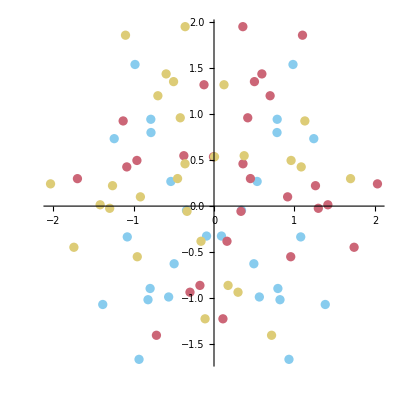

```mathematica
ListPlot[{totdata,totdata2,totdata3},AspectRatio->1]
```

```mathematica
nfakequant=Length[T@totdata]
```

2

```mathematica
testsample=testminusonedata[{T@totdata,T@totdata2,T@totdata3},{0,Table[0,{nfakequant}],Table[0,{nfakequant},{nfakequant}]},1000];
```

```mathematica
thisto0=Histogram3D[Chop[testsample[[;;,1;;2]]],{histbins},"Probability",Axes->True,AspectRatio->1,PlotRange->{{0,1.01},{0,1.01},{0,All}},Ticks->{Table[{i/100,ToString[i]<>"%"},{i,0,100,20}],Table[{i/100,ToString[i]<>"%"},{i,0,100,20}],Auto},AxesLabel->myaxes[{Subscript[p,AD],Subscript[p,MCI],P[p]}],ViewPoint->Dynamic[viewpoint]];
```

```mathematica
expng["testhisto0b",thisto0];
```

```mathematica
Mean[testsample]
```

{0.350177,0.32593,0.323893}

```mathematica
testsample=testminusonedata[{T@totdata,T@totdata2,T@totdata3},{0,Table[0,{nfakequant}],Table[0,{nfakequant},{nfakequant}]},1000];
```

```mathematica
thisto0=Histogram3D[Chop[testsample[[;;,1;;2]]],{histbins},"Probability",Axes->True,AspectRatio->1,PlotRange->{{0,1.01},{0,1.01},{0,All}},Ticks->{Table[{i/100,ToString[i]<>"%"},{i,0,100,20}],Table[{i/100,ToString[i]<>"%"},{i,0,100,20}],Auto},AxesLabel->myaxes[{Subscript[p,AD],Subscript[p,MCI],P[p]}],ViewPoint->Dynamic[viewpoint]];
```

```mathematica
expng["testhisto0",thisto0];
```